# CForm for uLG

Yoonkyung Eunnie Lee
2015.04.14

This version outputs L, M, N as a function of (P,L,x,y,z) 
Laguerre and Bessel Beams are discussed.

Note

M corresponds to a "Transverse" Field where Longitudinal component is zero, when a=[0,0,1]. 
E=∑M_PL(H=∑N_PL)  corresponds to TE mode, also called Azimuthal Polarization 
H=∑M_PL(E=∑N_PL)  corresponds to TM mode also called Radial Polarization 

Azimuthal Pol: best represented by Re(M)
Radial Pol: best represented by Im(N)

## Initialize

```mathematica
ClearAll["Global`*"];
t0=AbsoluteTime[];
$ProcessorCount
ParallelEvaluate[$ProcessID]

SetDirectory[NotebookDirectory[]];

line=4;
point=4;
(**)
tickthickness = 1.25;
fontstyle = {12, FontFamily -> "Helvetica"};
(**)
SetOptions[Plot, 
	ImageSize -> Large,
	LabelStyle -> fontstyle,
	Frame -> True,
	FrameTicksStyle -> AbsoluteThickness[tickthickness],
	AspectRatio -> 1,
	Axes -> False
];
(**)
SetOptions[VectorPlot, 
	ImageSize -> Medium,
	LabelStyle -> fontstyle,
	Frame -> True,
	FrameTicksStyle -> AbsoluteThickness[tickthickness],
     VectorPoints->20,VectorScale->{0.1,Scaled[0.9]},
	Axes -> False
];
(**)
SetOptions[ListPlot,
	ImageSize -> Medium,
	LabelStyle -> fontstyle,
	Frame -> True,
	AspectRatio -> 1,
	FrameTicksStyle -> AbsoluteThickness[tickthickness]
];
(**)
SetOptions[DensityPlot,
PlotPoints->50,
ColorFunction->"SunsetColors",
PlotRange->All,
Frame->False,
PlotRangePadding->0,
ImageSize->120,
(*AspectRatio->AutomaticImageSize,*)
Axes->None
];
```

8

{2515,2517,2518,2531,2558,2575,2607,2647}

## Scalar Helmholtz Eq. Solution u_G, u_LG (Gaussian, Laguerre-Gaussian)

### Parameters

```mathematica
(**************************************************************)
Clear[C0,ϵ0,μ0,λ,k,ω,zR,w0,alpha,beta]
SetAttributes[{C0,ϵ0,μ0,λ,k,ω,zR,w0},Constant];
SetAttributes[{alpha,beta},Constant];
wf[z_]=w0*Sqrt[1+z^2/zR^2]; 
RR[z_]=z*(1+zR^2/z^2); (* Radius of curvature *)
RRinvf[z_]=z/(z^2+zR^2);
ζ[z_]=ArcTan[zR,z];(* Gouy Phase Shift *)
Rho[x_,y_,z_]:=(Sqrt[2]*Sqrt[x^2+y^2])/wf[z];
Element[{P,L,x,y,z},Reals];
Element[{P,L},Integers];
Print["wf[z]: ",wf[z], ", RRinvf[z]:",RRinvf[z],", Rho[x,y,z]:",Rho[x,y,z]];
(**************************************************************)
```

wf[z]: w0 √(1+z^2/zR^2), RRinvf[z]:z/(z^2+zR^2), Rho[x,y,z]:(√2 √(x^2+y^2))/(w0 √(1+z^2/zR^2))

```mathematica
RRinvf[z]/z
```

1/(z^2+zR^2)

#### LaguerreL Function

```mathematica
(* For[i=0,i<5,i++,For[j=0,j<5,j++,Print["LaguerreL[0] at P=",i,", L=",j,"is : ",LaguerreL[i,Abs[j],0]];];]; *)
```

```mathematica
(* For[i=0,i<5,i++,For[j=0,j<5,j++,Print["LaguerreL[x] at P=",i,", L=",j,"is : ",LaguerreL[i,Abs[j],x]];];];*)
```

### Rule0 (group terms using Hold[]) Assumption0 (x,y,z∈Reals)

```mathematica
(**************************************************************)
(*Rule0 : w, ζ, 1/R, Rho *)
Clear[Rule0,A0]
Rule0={
Release[Rho[x,y,z]]->Hold[Rho[x,y,z]],
Release[Rho[x,y,z]^2]->Hold[Rho[x,y,z]]^2,
Release[1/Rho[x,y,z]]->1/Hold[Rho[x,y,z]],
Release[RRinvf[z]]->Hold[RRinvf[z]],
Release[1/RRinvf[z]]->1/Hold[RRinvf[z]],
Release[wf[z]]->Hold[wf[z]],
Release[wf[z]/w0]->Hold[wf[z]]/w0,
Release[1/wf[z]]->1/Hold[wf[z]],
Release[w0/wf[z]]->w0/Hold[wf[z]],
Release[wf[z]^2]->Hold[wf[z]]^2,
Release[1/wf[z]^2]->1/Hold[wf[z]]^2,

(1+z^2/zR^2)^(3/2)->Hold[wf[z]]^3/w0^3,
(1+z^2/zR^2)^2->Hold[wf[z]]^4/w0^4,
(1+z^2/zR^2)^(5/2)->Hold[wf[z]]^5/w0^5,
(1+z^2/zR^2)^3->Hold[wf[z]]^6/w0^6,

1/(1+z^2/zR^2)^(3/2)->w0^3/Hold[wf[z]]^3,
1/(1+z^2/zR^2)^2->w0^4/Hold[wf[z]]^4,
1/(1+z^2/zR^2)^(5/2)->w0^5/Hold[wf[z]]^5,
1/(1+z^2/zR^2)^3->w0^6/Hold[wf[z]]^6,

Release[ζ[z]]->Hold[ζ[z]]
};
A0={Element[{x,y,z},Reals]};
(**************************************************************)
```

### Scalar Solution for Simple Gaussian Beam u_G

```mathematica
(**************************************************************)
Clear[uG, IntensityG, PhaseG, uGSimp]
uG[x_,y_,z_]:=(w0/Hold[wf[z]])*Exp[(-(x^2+y^2)/(Hold[wf[z]])^2)-(I k ((x^2+y^2)*Hold[RRinvf[z]]/2))-I Hold[ ζ[z]]]*Exp[I k z];
DuG[x_,y_,z_]:=Module[{xx=x,yy=y,zz=z},Simplify[Grad[uG[xx,yy,zz],{xx,yy,zz}]]];
IntensityG[x_,y_,z_]=Abs[ReleaseHold[uG[x,y,z]]]^2;
PhaseG[x_,y_,z_]=Arg[ReleaseHold[uG[x,y,z]]];
Print["uG: ", ReleaseHold[uG[x,y,z]],"\n =",uG[x,y,z]];
(**************************************************************)
```

uG: (ⅇ^(ⅈ k z+(-x^2-y^2)/(w0^2 (1+z^2/zR^2))-(ⅈ k (x^2+y^2) z)/(2 (z^2+zR^2))-ⅈ ArcTan[zR,z]))/(√(1+z^2/zR^2))
 =(ⅇ^(ⅈ k z-1/2 ⅈ k (x^2+y^2) Hold[RRinvf[z]]+(-x^2-y^2)/Hold[wf[z]]^2-ⅈ Hold[ζ[z]]) w0)/Hold[wf[z]]

### Rule1 (evaluate derivatives of small functions and group terms) DSimpRule1 (simplify 1st order derivative of Rho and uLG) DSimpRule2 (simplify 2nd order derivative of Rho and uLG)

```mathematica
(**************************************************************)
(*Derivative of Rho*)
Clear[DRho0,DRho]
DRho0[x_,y_,z_]:=Assuming[A0,Grad[Rho[x,y,z],{x,y,z}]]
(* DRho[x_,y_,z_]:={(Sqrt[2]*x)/(Sqrt[x^2+y^2]*Hold[wf[z]]),(Sqrt[2]*y)/(Sqrt[x^2+y^2]*Hold[wf[z]]),-(Sqrt[2]*Sqrt[x^2+y^2]*Hold[RRinvf[z]])/Hold[wf[z]]}; *) 
DRho[x_,y_,z_]= DRho0[x,y,z]/.Rule0/.{Release[w0^2*Rho[x,y,z]/wf[z]^2]->w0^2*Hold[Rho[x,y,z]]/Hold[wf[z]]^2};
Print["DRho=",Release[DRho[x,y,z]],"=",DRho[x,y,z]];
```

DRho={(√2 x)/(w0 √(x^2+y^2) √(1+z^2/zR^2)),(√2 y)/(w0 √(x^2+y^2) √(1+z^2/zR^2)),-(√2 √(x^2+y^2) z)/(w0 (1+z^2/zR^2)^(3/2) zR^2)}={(√2 x)/(√(x^2+y^2) Hold[wf[z]]),(√2 y)/(√(x^2+y^2) Hold[wf[z]]),-(√2 w0^2 √(x^2+y^2) z)/(zR^2 Hold[wf[z]]^3)}

```mathematica
D[RRinvf[z],z]; 
D[ζ[z],z];
D[wf[z],z];
DRRinvf[z_]=-2 Hold[RRinvf[z]]^2 + Hold[RRinvf[z]]/z;
Dζ[z_]=Hold[RRinvf[z]]*zR/z;
Dwf[z_]=w0^2*z/zR^2/Hold[wf[z]];
Print["DRRinvf[z]=" ,DRRinvf[z],"="Release[DRRinvf[z]],"\n",
"Dζ[z]=",Dζ[z],"=",Release[Dζ[z]],"\n",
"Dwf[z]=",Dwf[z],"=",Release[Dwf[z]],"\n",
"\n",
"DRRinvf[z]-(d RRinvf[z])/dz=" , Simplify[Release[DRRinvf[z]-D[RRinvf[z],z]]], 
", Dζ[z]-(d ζ[z])/dz=", Simplify[Release[Dζ[z]-D[ζ[z],z]]],
", Dwf[z]-(d wf[z])/dz=", Simplify[Release[Dwf[z]-D[wf[z],z]] ] 
]; 
(**************************************************************)
(*Rule1 : Dw, Dζ, D(1/R), D(Rho), D(uG)*)
Rule1={D[Hold[RRinvf[z]],z]->DRRinvf[z],
D[Hold[ζ[z]],z]->Dζ[z],
D[Hold[wf[z]],z]->Dwf[z],
Release[DRRinvf[z]]-> DRRinvf[z],
Release[Dζ[z]]->Dζ[z],
Release[Dwf[z]]->Dwf[z],
Release[DRho[x,y,z]]->DRho[x,y,z]
};
(**************************************************************)
DuGRatio[x_,y_,z_]=Simplify[Release[DuG[x,y,z]/uG[x,y,z]]/.Rule1//.Rule0];
(**************************************************************)
(*DSimpRule1: Simplify 1st order Derivatives of uG and Rho*)
DSimpRule1={
D[Hold[Rho[x,y,z]],x]-> DRho[x,y,z][[1]],
D[Hold[Rho[x,y,z]],y]-> DRho[x,y,z][[2]],
D[Hold[Rho[x,y,z]],z]-> DRho[x,y,z][[3]],
D[Hold[uG[x,y,z]],x]-> DuGRatio[x,y,z][[1]] Hold[uG[x,y,z]],
D[Hold[uG[x,y,z]],y]-> DuGRatio[x,y,z][[2]] Hold[uG[x,y,z]],
D[Hold[uG[x,y,z]],z]-> DuGRatio[x,y,z][[3]] Hold[uG[x,y,z]]
};
(**************************************************************)
(*DSimpRule2: Simplify 2nd order Derivatives of uG and Rho*)
DSimpRule2={
D[Hold[Rho[x,y,z]],x,z]->Release[D[DRho[x,y,z][[1]],z]]//.Rule0,
D[Hold[Rho[x,y,z]],y,z]->Release[D[DRho[x,y,z][[2]],z]]//.Rule0,
D[Hold[Rho[x,y,z]],{x,2}]->D[DRho[x,y,z][[1]],x],
D[Hold[Rho[x,y,z]],{y,2}]->D[DRho[x,y,z][[2]],y],
D[Hold[uG[x,y,z]],x,z]->Release[D[DuGRatio[x,y,z][[1]] Hold[uG[x,y,z]],z]]//.Rule1//.Rule0,
D[Hold[uG[x,y,z]],y,z]->Release[D[DuGRatio[x,y,z][[2]] Hold[uG[x,y,z]],z]]//.Rule1//.Rule0,
D[Hold[uG[x,y,z]],{x,2}]->Simplify[D[DuGRatio[x,y,z][[1]] Hold[uG[x,y,z]],x]/.DSimpRule1],
D[Hold[uG[x,y,z]],{y,2}]->Simplify[D[DuGRatio[x,y,z][[2]] Hold[uG[x,y,z]],y]/.DSimpRule1]
};
```

DRRinvf[z]=Hold[RRinvf[z]]/z-2 Hold[RRinvf[z]]^2= (-(2 z^2)/((z^2+zR^2)^2)+1/(z^2+zR^2))
Dζ[z]=(zR Hold[RRinvf[z]])/z=zR/(z^2+zR^2)
Dwf[z]=(w0^2 z)/(zR^2 Hold[wf[z]])=(w0 z)/(√(1+z^2/zR^2) zR^2)

DRRinvf[z]-(d RRinvf[z])/dz=0, Dζ[z]-(d ζ[z])/dz=0, Dwf[z]-(d wf[z])/dz=0

### Scalar Solution for Laguerre Gaussian Beam u_LG with e^iLϕ

```mathematica
(*CnormLG[P_,L_]:=Sqrt[2 Factorial[P]/(Pi*(w0^2)*Factorial[P+Abs[L]])]*)
CnormLG[P_,L_]:=Cnorm;
SetAttributes[{Cnorm},Constant];
(*Expressed using uG*)
uLG[P_,L_,x_,y_,z_]:=CnormLG[P,L]*(Hold[Rho[x,y,z]])^(Abs[L])*LaguerreL[P,Abs[L],(Hold[Rho[x,y,z]])^2]*Exp[I L ArcTan[x,y]]*Exp[-I (2 P+Abs[L]) ζ[z]]*Hold[uG[x,y,z]];
DuLG[P_,L_,x_,y_,z_]:=Module[{xx=x,yy=y,zz=z},Simplify[Grad[uLG[P,L,xx,yy,zz],{xx,yy,zz}]]];
IntensityLG[P_,L_,x_,y_,z_]:=Abs[ReleaseHold[ReleaseHold[uLG[P,L,x,y,z]]]]^2;
PhaseLG[P_,L_,x_,y_,z_]:=Arg[ReleaseHold[ReleaseHold[uLG[P,L,x,y,z]]]];
Print["uLG: ",ReleaseHold[ReleaseHold[uLG[P,L,x,y,z]]]];
```

uLG: 1/(√(1+z^2/zR^2))2^(Abs[L]/2) Cnorm ⅇ^(ⅈ k z+(-x^2-y^2)/(w0^2 (1+z^2/zR^2))-(ⅈ k (x^2+y^2) z)/(2 (z^2+zR^2))+ⅈ L ArcTan[x,y]-ⅈ ArcTan[zR,z]-ⅈ (2 P+Abs[L]) ArcTan[zR,z]) ((√(x^2+y^2))/(w0 √(1+z^2/zR^2)))^Abs[L] LaguerreL[P,Abs[L],(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))]

## Vector Helmholtz Eq. Solution L,M,N using ψ=u_G, u_LG

### a = [0,0,1]

```mathematica
Clear[avec,kvec]
avec = {0,0,1};  (*unit vector in arbiary direction, determines polarization*)
kvec={0,0,k};  (*propagation direction*)
```

### L, M, N with e^iLϕ

```mathematica
(**************************************************************)
(* Theory reference is Stratton E&M, Chapter VII *)
Clear[ψ,Lvec,Mvec,Nvec]
(*Derivatives will be taken in xyz. *) 
(*First define ψ *) 
ψ[P_,L_,x_,y_,z_] := uLG[P,L,x,y,z];
(*Compute L, M, N*)
Lvec[P_,L_,x_,y_,z_]:= Grad[ ψ[P,L,x,y,z] ,{x,y,z}]
Mvec[P_,L_,x_,y_,z_]:= Curl[avec*ψ[P,L,x,y,z],{x,y,z}]
Nvec[P_,L_,x_,y_,z_]:= Curl[Mvec[P,L,x,y,z]  ,{x,y,z}]/k 
(*Vector Equality*)
Print["Vector Equality\n ∇×L=",Simplify[Curl[Lvec[P,L,x,y,z],{x,y,z}]],
",∇.M=",Simplify[Div[Mvec[P,L,x,y,z],{x,y,z}]],
",∇.N=",Simplify[Div[Nvec[P,L,x,y,z],{x,y,z}]],
",L*M=",Simplify[Dot[Lvec[P,L,x,y,z],Mvec[P,L,x,y,z]]],
",M-L×a=",Simplify[Mvec[P,L,x,y,z]-Cross[Lvec[P,L,x,y,z],avec]]
]
(**************************************************************)
```

Vector Equality
 ∇×L={0,0,0},∇.M=0,∇.N=0,L*M=0,M-L×a={0,0,0}

#### Show Mvec, Nvec : Full Formula

```mathematica
(* MvecFull=Simplify[Mvec[PP,LL,x,y,z]//.DSimpRule1//.Rule0] *)
```

```mathematica
MvecFull={1/((x^2+y^2)^(3/2) Hold[wf[z]]^2)Cnorm ⅇ^(ⅈ (LL ArcTan[x,y]-(2 PP+Abs[LL]) Hold[ζ[z]])) Hold[Rho[x,y,z]]^(-1+Abs[LL]) Hold[uG[x,y,z]] (-2 √2 y (x^2+y^2) Hold[Rho[x,y,z]]^2 Hold[wf[z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+√2 y (x^2+y^2) Abs[LL] Hold[wf[z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]-ⅈ √(x^2+y^2) Hold[Rho[x,y,z]] (-2 ⅈ y (x^2+y^2)+(-LL x+k y (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]),1/((x^2+y^2)^(3/2) Hold[wf[z]]^2)Cnorm ⅇ^(ⅈ (LL ArcTan[x,y]-(2 PP+Abs[LL]) Hold[ζ[z]])) Hold[Rho[x,y,z]]^(-1+Abs[LL]) Hold[uG[x,y,z]] (2 √2 x (x^2+y^2) Hold[Rho[x,y,z]]^2 Hold[wf[z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-√2 x (x^2+y^2) Abs[LL] Hold[wf[z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+√(x^2+y^2) Hold[Rho[x,y,z]] (2 x (x^2+y^2)+ⅈ (LL y+k x (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]),0};
```

```mathematica
(* NvecFull=Simplify[Nvec[PP,LL,x,y,z]//.DSimpRule2//.DSimpRule1//.Rule1//.Rule0] *)
```

```mathematica
NvecFull={1/(2 k z zR^2)Cnorm ⅇ^(ⅈ (LL ArcTan[x,y]-(2 PP+Abs[LL]) Hold[ζ[z]])) Hold[Rho[x,y,z]]^Abs[LL] (-1/Hold[wf[z]]^4 16 w0^2 x z^2 Hold[Rho[x,y,z]]^2 Hold[uG[x,y,z]] LaguerreL[-2+PP,2+Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^4 8 w0^2 x z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^4 8 w0^2 x z^2 (1+Abs[LL]) Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+(4 √2 w0^2 x z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[wf[z]]^3)-(4 ⅈ √2 LL w0^2 y z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[wf[z]]^3)+1/(√(x^2+y^2) Hold[wf[z]])4 ⅈ √2 x zR^3 (2 PP+Abs[LL]) Hold[Rho[x,y,z]] Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-1/Hold[wf[z]]^5 4 ⅈ √2 w0^2 x √(x^2+y^2) z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] (-2 ⅈ+k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-1/(√(x^2+y^2) Hold[wf[z]]^5)2 ⅈ √2 x Hold[Rho[x,y,z]] Hold[uG[x,y,z]] (-4 ⅈ w0^2 (x^2+y^2) z^2+2 ⅈ w0^2 z^2 Hold[wf[z]]^2-zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-1/(x^2+y^2)2 LL y zR^3 (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]-(4 w0^2 x z^2 (-1+Abs[LL]) Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(Hold[Rho[x,y,z]]^2 Hold[wf[z]]^4)-(2 √2 w0^2 x z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^3)+(2 ⅈ √2 LL w0^2 y z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^3)-(2 ⅈ √2 x zR^3 Abs[LL] (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]])+(2 √2 w0^2 x √(x^2+y^2) z^2 Abs[LL] Hold[uG[x,y,z]] (2+ⅈ k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(Hold[Rho[x,y,z]] Hold[wf[z]]^5)-1/Hold[wf[z]]^2 2 x zR^3 (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] (-2 ⅈ+k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^5)ⅈ √2 x Abs[LL] Hold[uG[x,y,z]] (-4 ⅈ w0^2 (x^2+y^2) z^2+2 ⅈ w0^2 z^2 Hold[wf[z]]^2-zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/((x^2+y^2) Hold[wf[z]]^4)LL y Hold[uG[x,y,z]] (-4 ⅈ w0^2 (x^2+y^2) z^2+2 ⅈ w0^2 z^2 Hold[wf[z]]^2-zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^7 ⅇ^(-(ⅈ (-2 ⅈ (x^2+y^2)+Hold[wf[z]]^2 (-2 k z+k (x^2+y^2) Hold[RRinvf[z]]+2 Hold[ζ[z]])))/(2 Hold[wf[z]]^2)) w0 x (-8 w0^2 (x^2+y^2) z^2-4 ⅈ w0^2 z^2 (3 ⅈ+k (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2+2 ⅈ (-2 k z zR^2+(2 zR^3+k (w0^2 z^2+(x^2+y^2) zR^2)) Hold[RRinvf[z]]-2 k (x^2+y^2) z zR^2 Hold[RRinvf[z]]^2) Hold[wf[z]]^4+k zR^2 Hold[RRinvf[z]] (-2 ⅈ+2 k z-(k (x^2+y^2)+2 (-2 ⅈ z+zR)) Hold[RRinvf[z]]+2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^6) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]),1/(2 k z zR^2)Cnorm ⅇ^(ⅈ (LL ArcTan[x,y]-(2 PP+Abs[LL]) Hold[ζ[z]])) Hold[Rho[x,y,z]]^Abs[LL] (-1/Hold[wf[z]]^4 16 w0^2 y z^2 Hold[Rho[x,y,z]]^2 Hold[uG[x,y,z]] LaguerreL[-2+PP,2+Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^4 8 w0^2 y z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^4 8 w0^2 y z^2 (1+Abs[LL]) Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+(4 ⅈ √2 LL w0^2 x z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[wf[z]]^3)+(4 √2 w0^2 y z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[wf[z]]^3)+1/(√(x^2+y^2) Hold[wf[z]])4 ⅈ √2 y zR^3 (2 PP+Abs[LL]) Hold[Rho[x,y,z]] Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-1/Hold[wf[z]]^5 4 ⅈ √2 w0^2 y √(x^2+y^2) z^2 Hold[Rho[x,y,z]] Hold[uG[x,y,z]] (-2 ⅈ+k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-1/(√(x^2+y^2) Hold[wf[z]]^5)2 ⅈ √2 y Hold[Rho[x,y,z]] Hold[uG[x,y,z]] (-4 ⅈ w0^2 (x^2+y^2) z^2+2 ⅈ w0^2 z^2 Hold[wf[z]]^2-zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+1/(x^2+y^2)2 LL x zR^3 (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]-(4 w0^2 y z^2 (-1+Abs[LL]) Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(Hold[Rho[x,y,z]]^2 Hold[wf[z]]^4)-(2 ⅈ √2 LL w0^2 x z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^3)-(2 √2 w0^2 y z^2 Abs[LL] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^3)-(2 ⅈ √2 y zR^3 Abs[LL] (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]])+(2 √2 w0^2 y √(x^2+y^2) z^2 Abs[LL] Hold[uG[x,y,z]] (2+ⅈ k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])/(Hold[Rho[x,y,z]] Hold[wf[z]]^5)-1/Hold[wf[z]]^2 2 y zR^3 (2 PP+Abs[LL]) Hold[RRinvf[z]] Hold[uG[x,y,z]] (-2 ⅈ+k Hold[RRinvf[z]] Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/(√(x^2+y^2) Hold[Rho[x,y,z]] Hold[wf[z]]^5)ⅈ √2 y Abs[LL] Hold[uG[x,y,z]] (-4 ⅈ w0^2 (x^2+y^2) z^2+2 ⅈ w0^2 z^2 Hold[wf[z]]^2-zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/((x^2+y^2) Hold[wf[z]]^4)LL x Hold[uG[x,y,z]] (4 ⅈ w0^2 (x^2+y^2) z^2-2 ⅈ w0^2 z^2 Hold[wf[z]]^2+zR^2 (-2 k z+(k (x^2+y^2)+2 zR) Hold[RRinvf[z]]-2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^4) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+1/Hold[wf[z]]^7 ⅇ^(-(ⅈ (-2 ⅈ (x^2+y^2)+Hold[wf[z]]^2 (-2 k z+k (x^2+y^2) Hold[RRinvf[z]]+2 Hold[ζ[z]])))/(2 Hold[wf[z]]^2)) w0 y (-8 w0^2 (x^2+y^2) z^2-4 ⅈ w0^2 z^2 (3 ⅈ+k (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2+2 ⅈ (-2 k z zR^2+(2 zR^3+k (w0^2 z^2+(x^2+y^2) zR^2)) Hold[RRinvf[z]]-2 k (x^2+y^2) z zR^2 Hold[RRinvf[z]]^2) Hold[wf[z]]^4+k zR^2 Hold[RRinvf[z]] (-2 ⅈ+2 k z-(k (x^2+y^2)+2 (-2 ⅈ z+zR)) Hold[RRinvf[z]]+2 k (x^2+y^2) z Hold[RRinvf[z]]^2) Hold[wf[z]]^6) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]),1/(k (x^2+y^2)^(3/2) Hold[wf[z]]^4)Cnorm ⅇ^(ⅈ (LL ArcTan[x,y]-(2 PP+Abs[LL]) Hold[ζ[z]])) Hold[Rho[x,y,z]]^(-2+Abs[LL]) Hold[uG[x,y,z]] (-8 (x^2+y^2)^(3/2) Hold[Rho[x,y,z]]^4 Hold[wf[z]]^2 LaguerreL[-2+PP,2+Abs[LL],Hold[Rho[x,y,z]]^2]+2 √2 (x^2+y^2) Hold[Rho[x,y,z]]^3 Hold[wf[z]] (-4 (x^2+y^2)+(1-2 ⅈ k (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2) LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]-2 (x^2+y^2)^(3/2) (-1+Abs[LL]) Abs[LL] Hold[wf[z]]^2 LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+√2 (x^2+y^2) Abs[LL] Hold[Rho[x,y,z]] Hold[wf[z]] (4 (x^2+y^2)+ⅈ (ⅈ+2 k (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2) LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+√(x^2+y^2) Hold[Rho[x,y,z]]^2 (-4 (x^2+y^2)^2 LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+(LL^2+2 ⅈ k (x^2+y^2) Hold[RRinvf[z]]+k^2 (x^2+y^2)^2 Hold[RRinvf[z]]^2) Hold[wf[z]]^4 LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]+4 (x^2+y^2) Hold[wf[z]]^2 (LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+2 Abs[LL] LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]+LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]-ⅈ k (x^2+y^2) Hold[RRinvf[z]] LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2])))};
```

## Plots

### Plot Constants & Simplify Rule

```mathematica
(**************************************************************)
(*Constants Required for Plotting*)
nMedium=1;  (*Index of the medium *)
λ=1.0*10^-6;   (*wavelength*)
k=nMedium*2Pi/λ; (*wavevector*)
w0=2.0*10^-6; (*waist radius 2 microns*)
zR=Pi w0^2/λ ; (* Rayleign Range *)
(**************************************************************)
```

```mathematica
(**************************************************************)
PlotSimpRule={
nMedium-> 1,  (*Index of the medium *)
λ->1.0*10^-6,   (*wavelength*)
k->nMedium*2Pi/λ, (*wavevector*)
w0->2.0*10^-6, (*waist radius 2 microns*)
zR->Pi w0^2/λ,  (* Rayleign Range *)
(*Choose XP for Display*) 
(*
alpha->y/Sqrt[x^2+y^2],
beta->-x/Sqrt[x^2+y^2] ,
*) 
(*
alpha->1/Sqrt[2],beta->I/Sqrt[2],
*)
(**)
Z-> 376.73,
Cnorm->Sqrt[2 Factorial[P]/(Pi*(w0^2)*Factorial[P+Abs[L]])]
};
```

### Plots for uG

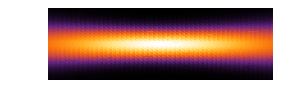

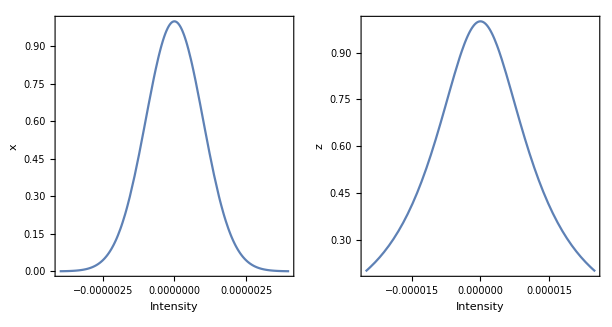

```mathematica
plot1=DensityPlot[IntensityG[x,y,0],{x,-2 w0,2 w0},{y,-2 w0,2 w0},ImageSize->120 ];
plot2=DensityPlot[IntensityG[x,0,z],{z,-zR, zR},{x,-2 w0,2w0} ,ImageSize->300,AspectRatio->Automatic  ,AxesLabel->{"z","x"}];
GraphicsRow[{plot1,plot2},Background->Black,Spacings->0,Alignment->{Center,Center}]
Export["uG_Intensity.jpg",%,"JPEG"];
plot3=Plot[IntensityG[x,0,0],{x,-2w0,2w0},ImageSize->300  ,AxesLabel->{"Intensity","x"}];
plot4=Plot[IntensityG[0,0,z],{z,-2zR,2zR},ImageSize->300  ,AxesLabel->{"Intensity","z"}];
GraphicsRow[{plot3,plot4},Spacings->0,Alignment->{Center,Center}]
Export["uG_Intensity1D.jpg",%,"JPEG"];
(**************************************************************)
```

### Plots for uLG

#### Plot for uLG, P=2, L=1;

```mathematica
Clear[P0,L0]
P0=2; L0=1;
PLSimp={P->P0,L->L0};
```

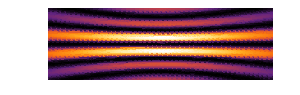

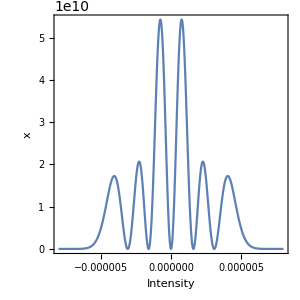

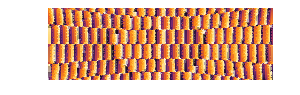

```mathematica
plotLG1=DensityPlot[IntensityLG[P,L,x,y,0]//.PlotSimpRule//.PLSimp,{x,-2 w0,2 w0},{y,-2 w0,2 w0},ImageSize->120];
plotLG2=DensityPlot[IntensityLG[P,L,x,0,z]//.PlotSimpRule//.PLSimp,{z,-zR,zR},{x,-2 w0,2 w0},ImageSize->300,AspectRatio->Automatic,AxesLabel->{"z","x"}];
GraphicsRow[{plotLG1,plotLG2},Background->Black,Spacings->0,Alignment->{Center,Center}]
Export["uLG21_Intensity.jpg",%,"JPEG"];
plotLG3=Plot[IntensityLG[P,L,x,0,0]//.PlotSimpRule//.PLSimp,{x,-4 w0,4 w0},ImageSize->300,AxesLabel->{"Intensity","x"}]
Export["uLG21_Intensity1D.jpg",%,"JPEG"];
(**************************************************************)
plotLG5=DensityPlot[PhaseLG[P,L,x,y,0]//.PlotSimpRule//.PLSimp,{x,-2 w0,2 w0},{y,-2 w0,2 w0},ImageSize->120, PlotPoints->30];
plotLG6=DensityPlot[PhaseLG[P,L,x,0,z]//.PlotSimpRule//.PLSimp,{z,-zR, zR},{x,-2 w0,2w0} ,ImageSize->300,AspectRatio->Automatic  ,AxesLabel->{"z","x"}];
GraphicsRow[{plotLG5,plotLG6},Background->Black,Spacings->0,Alignment->{Center,Center}]
Export["uLG21_Phase.jpg",%,"JPEG"];
```

#### More Plots for uLG

```mathematica
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[IntensityLG[P,L,x,y,0]]//.PlotSimpRule,{x,-4 w0,4 w0},{y,-4 w0,4 w0},Mesh->None,PlotPoints->50,ColorFunction->"SunsetColors",PlotRange->All,Frame->False,ImageSize->120 {1,1},PlotRangePadding->0],{P,0,2},{L,0,3}],Spacings->0,Background->Black]
Export["uLG_table_Intensity.jpg",%,"JPEG"];
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[PhaseLG[P,L,x,y,0]]//.PlotSimpRule,{x,-4 w0,4 w0},{y,-4 w0,4 w0},Mesh->None,PlotPoints->50,ColorFunction->"SunsetColors",PlotRange->All,Frame->False,ImageSize->120 {1,1},PlotRangePadding->0],{P,0,2},{L,0,3}],Spacings->0,Background->Black]
Export["uLG_table_Phase.jpg",%,"JPEG"];
```

-Graphics-

-Graphics-

### Plots for Vector Fields M, N

#### Evaluate M,N

```mathematica
(**************************************************************)
Mveceval[P_,L_,x0_,y0_,z0_]:=Assuming[A0,Simplify[ReleaseHold[ReleaseHold[Mvec[P,L,x,y,z]]]//.{x->x0,y->y0,z->z0}//.{Cnorm-> Sqrt[2 Factorial[P]/(Pi*(w0^2)*Factorial[P+Abs[L]])]}]];
(**************************************************************)
Nveceval[P_,L_,x0_,y0_,z0_]:=Simplify[ReleaseHold[ReleaseHold[Nvec[P,L,x,y,z]]]//.{x->x0,y->y0,z->z0}//.{Cnorm-> Sqrt[2 Factorial[P]/(Pi*(w0^2)*Factorial[P+Abs[L]])]}];
Clear[P0,L0]
PLSimp={P->P0,L->L0};
(**************************************************************)
```

#### Plot: 2D (xy), vector plot of Re(M), Re(N)

```mathematica
Clear[Mxy,Nxy]
Mxy[P_,L_]={Re[Mveceval[P,L,x,y,0][[1]]],Re[Mveceval[P,L,x,y,0][[2]]]};
Nxy[P_,L_]=If[P==0,
{Re[Nveceval[0,L,x,y,0][[1]]],Re[Nveceval[0,L,x,y,0][[2]]]},
{Re[Nveceval[P,L,x,y,0][[1]]],Re[Nveceval[P,L,x,y,0][[2]]]}
];
Print["M Vector on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[VectorPlot[Evaluate[Mxy[P0,L0]],{x,-2 w0,2 w0},{y,-2 w0,2 w0},Frame->False,ImageSize->180 {1,1},VectorStyle->{Red},Mesh->None],{P0,0,2},{L0,0,3}],Spacings->0]
Export["Mxy_table_P0-2L0-3.jpg",%,"JPEG"];
Print["N Vector on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[VectorPlot[Evaluate[Nxy[P0,L0]],{x,-2 w0,2 w0},{y,-2 w0,2 w0},Frame->False,ImageSize->180 {1,1},VectorStyle->{Blue},Mesh->None],{P0,0,2},{L0,0,3}],Spacings->0]
Export["Nxy_table_P0-2L0-3.jpg",%,"JPEG"];
```

M Vector on xy, a=(0,0,1)

-Graphics-

N Vector on xy, a=(0,0,1)

-Graphics-

#### Plot: 2D (xy), vector plot of Im(M), Im(N)

```mathematica
Clear[MxyIm,NxyIm]
MxyIm[P_,L_]={Im[Mveceval[P,L,x,y,0][[1]]],Im[Mveceval[P,L,x,y,0][[2]]]};
NxyIm[P_,L_]=If[P==0,
{Im[Nveceval[0,L,x,y,0][[1]]],Im[Nveceval[0,L,x,y,0][[2]]]},
{Im[Nveceval[P,L,x,y,0][[1]]],Im[Nveceval[P,L,x,y,0][[2]]]}
];
Print["Im[M] Vector on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[VectorPlot[Evaluate[MxyIm[P0,L0]],{x,-2 w0,2 w0},{y,-2 w0,2 w0},Frame->False,ImageSize->180 {1,1},VectorStyle->{Red},Mesh->None],{P0,0,2},{L0,0,3}],Spacings->0]
Export["MxyIm_table_P0-2L0-3.jpg",%,"JPEG"];
Print["Im[N] Vector on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[VectorPlot[Evaluate[NxyIm[P0,L0]],{x,-2 w0,2 w0},{y,-2 w0,2 w0},Frame->False,ImageSize->180 {1,1},VectorStyle->{Blue},Mesh->None],{P0,0,2},{L0,0,3}],Spacings->0]
Export["NxyIm_table_P0-2L0-3.jpg",%,"JPEG"];
```

Im[M] Vector on xy, a=(0,0,1)

-Graphics-

Im[N] Vector on xy, a=(0,0,1)

-Graphics-

#### Plot: Amplitude of M, N

```mathematica
Clear[P0,L0]
PLSimp={P->P0,L->L0};
Clear[MI,NI]
MI[P_,L_]=Norm[Mveceval[P,L,x,y,z],2];
NI[P_,L_]=If[P==0,
Norm[Nveceval[0,L,x,y,z],2],
Norm[Nveceval[P,L,x,y,z],2]
];
```

```mathematica
(**************************************************************)
Print["|M| on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[MI[P0,L0]//.z->0],{x,-4 w0,4 w0},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Background->Black,Alignment->{Center,Center}]
Export["Mintensity_table_xy_P0-2L0-3.jpg",%,"JPEG"];
```

|M| on xy, a=(0,0,1)

-Graphics-

```mathematica
(**************************************************************)
Print["|M| on yz, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[MI[P0,L0]//.x->0],{z,-zR,zR},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Background->Black,Alignment->{Center,Center}]
Export["Mintensity_table_yz_P0-2L0-3.jpg",%,"JPEG"];
```

|M| on yz, a=(0,0,1)

-Graphics-

```mathematica
(**************************************************************)
Print["|N| on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[NI[P0,L0]//.z->0],{x,-4 w0,4 w0},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Background->Black,Alignment->{Center,Center}]
Export["Nintensity_table_xy_P0-2L0-3.jpg",%,"JPEG"];
```

|N| on xy, a=(0,0,1)

-Graphics-

```mathematica
(**************************************************************)
Print["|N| on yz, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[NI[P0,L0]//.x->0],{z,-zR,zR},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Background->Black,Alignment->{Center,Center}]
Export["Nintensity_table_yz_P0-2L0-3.jpg",%,"JPEG"];
```

|N| on yz, a=(0,0,1)

-Graphics-

#### Plot: Phase of M, N

```mathematica
Mveceval[P,L,x,y,z][[3]]
```

0

```mathematica
Clear[NzRe, NzIm, NzArg]
NzRe[P_,L_]=If[P==0,
Re[Nveceval[0,L,x,y,z][[3]]],
Re[Nveceval[P,L,x,y,z][[3]]]
];
NzIm[P_,L_]=If[P==0,
Im[Nveceval[0,L,x,y,z][[3]]],
Im[Nveceval[P,L,x,y,z][[3]]]
];
NzArg[P_,L_]=If[P==0,
Arg[Nveceval[0,L,x,y,z][[3]]],
Arg[Nveceval[P,L,x,y,z][[3]]]
];
```

```mathematica
(**************************************************************)
Print["NzRe on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[NzRe[P0,L0]//.z->0],{x,-4 w0,4 w0},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzRe_table_xy_P0-2L0-3.jpg",%,"JPEG"];
```

NzRe on xy, a=(0,0,1)

-Graphics-

```mathematica
(**************************************************************)
Print["NzIm on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[NzIm[P0,L0]//.z->0],{x,-4 w0,4 w0},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0,Alignment->{Center,Center}]
Export["NzIm_table_xy_P0-2L0-3.jpg",%,"JPEG"];
```

NzIm on xy, a=(0,0,1)

-Graphics-

```mathematica
(**************************************************************)
Print["NzArg on xy, a=(0,0,1)"]
GraphicsGrid[ParallelTable[DensityPlot[Evaluate[NzArg[P0,L0]//.z->0],{x,-4 w0,4 w0},{y,-4 w0,4 w0},Frame->False,AspectRatio->Automatic  ,ImageSize->180 ,ColorFunction->"SunsetColors",PlotRange->All],{P0,0,2},{L0,0,3}],Spacings->0, Alignment->{Center,Center}]
Export["NzArg_table_xy_P0-2L0-3.jpg",%,"JPEG"];
```

NzArg on xy, a=(0,0,1)

-Graphics-

### Clear variables and free memory

```mathematica
Clear[λ,k,w0,zR] 
Clear[plot1, plot2, plot3, plot4]
Clear[plotLG1, plotLG2, plotLG3, plotLG4, plotLG5, plotLG6]
```

## Output using CForm

```mathematica
Limit[NvecFull,z->0]
```

$Aborted

### CFormRule1, CFormRule2

```mathematica
(**************************************************************)(*Rules for Simplification*)(*in NvecFull and MvecFull,the following Hold forms exist.*)(*Hold[wf[z]],Hold[Rho[x,y,z]],Hold[ζ[z]],Hold[uG[x,y,z]],Hold[RRinvf[z]]*)(*Additionally,the following can be simplified*)(*x^2+y^2,ArcTan[x,y],Abs[L],LaguerreL[P,Abs[L],Hold[Rho[x,y,z]]^2]*)(**************************************************************)(*SimplifyRule1:Simplify DuG,DRho*)Clear[CFormRule1,CFormRule2,w,zeta,RRinv]
CFormRule1={LaguerreL[-2+PP,2+Abs[LL],Hold[Rho[x,y,z]]^2]->LagPm2,LaguerreL[-1+PP,1+Abs[LL],Hold[Rho[x,y,z]]^2]->LagPm1,LaguerreL[PP,Abs[LL],Hold[Rho[x,y,z]]^2]->LagP,Hold[uG[x,y,z]]->uG,Hold[Rho[x,y,z]]->Rho,Hold[wf[z]]->w,Hold[ζ[z]]->zeta,Hold[RRinvf[z]]->RRinv,ArcTan[x,y]->Phi,Abs[L]->Labs,Abs[LL]->Labs,x^2+y^2->r^2,-x^2-y^2->-r^2};
(**************************************************************)
(*CFormRule2:Re-introduces RRinv,and creates squared variables*)

CFormRule2={z^2->z2,r^2->r2,w^2->w2,1/r^2->1/r2,Sqrt[r2]->r,1/Sqrt[r2]->1/r,1/w^2->1/w2,x^2->x2,y^2->y2};
(**************************************************************)
```

### Output C Form: 1. Nonsingular

```mathematica
Clear[uGout]
uGout=uG[x,y,z]//.CFormRule1;
Clear[MvecC,NvecC,NvecCz0,NvecCa,NvecCb]
MvecC=Assuming[{r≥0},Simplify[MvecFull//.CFormRule1]];
NvecC=Collect[Assuming[{r≥0},Simplify[NvecFull//.CFormRule1]],{LagP,LagPm1,LagPm2}];
```

```mathematica
NvecCz0=Collect[Simplify[NvecC//.{RRinv-> z/(z^2+zR^2)}],z];
NvecCz0=FullSimplify[NvecCz0//.{z->0,w->w0,zeta->0,uG->ⅇ^(-r^2/w0^2)}];
```

```mathematica
NvecCz0
```

{1/(2 k r^2 w0^2 zR^2)ⅈ Cnorm ⅇ^(ⅈ LL Phi-r^2/w0^2) Rho^(-1+Labs) (2 (1+Labs+2 PP) (r (2 LagP r Rho-√2 Labs LagP w0+2 √2 LagPm1 Rho^2 w0) x+ⅈ LagP LL Rho w0^2 y) zR+ⅈ k LagP LL Rho w0^2 y (r^2-2 zR^2)+k r x (-√2 Labs LagP w0 (r^2-2 zR^2)+2 √2 LagPm1 Rho^2 w0 (r^2-2 zR^2)+2 LagP r Rho (r^2-w0^2-2 zR^2))),1/(2 k r^2 w0^2 zR^2)Cnorm ⅇ^(ⅈ LL Phi-r^2/w0^2) Rho^(-1+Labs) (2 (1+Labs+2 PP) (LagP LL Rho w0^2 x+ⅈ r (2 LagP r Rho-√2 Labs LagP w0+2 √2 LagPm1 Rho^2 w0) y) zR+k LagP LL Rho w0^2 x (r^2-2 zR^2)+ⅈ k r y (-√2 Labs LagP w0 (r^2-2 zR^2)+2 √2 LagPm1 Rho^2 w0 (r^2-2 zR^2)+2 LagP r Rho (r^2-w0^2-2 zR^2))),1/(k r^2 w0^4)Cnorm ⅇ^(ⅈ LL Phi-r^2/w0^2) Rho^(-2+Labs) (-4 LagP r^4 Rho^2+4 √2 r^3 Rho (Labs LagP-2 LagPm1 Rho^2) w0+2 r^2 (-(-1+Labs) Labs LagP+2 (LagP+LagPm1+2 Labs LagPm1) Rho^2-4 LagPm2 Rho^4) w0^2+√2 r Rho (-Labs LagP+2 LagPm1 Rho^2) w0^3+LagP LL^2 Rho^2 w0^4)}

### Output C Form: 2. Singular (at x=y=0)

```mathematica
(* Construct a rule for x=y=0 to avoid INF or NAN *) 
(* MvecSimp (full forms) -> ZeroSimpRule -> Mvec0 -> CFormRule*) 
(* Additionally, LaguerreL[PP,1,0]=PP+1 *)
```

#### uG and uLG at x=y=0

```mathematica
uG0=uG[0,0,z]
uLG0=Limit[ReleaseHold[uLG[0,0,x,0,z]],x->0]//.Rule0;
uG0out=uG[0,0,z]//.CFormRule1;
```

(ⅇ^(ⅈ k z-ⅈ Hold[ζ[z]]) w0)/Hold[wf[z]]

#### M and N at x=y=0

```mathematica
(*For Limits, approach from the positive x axis.*)
```

```mathematica
(**************************************************************)
MvecSimp[P_,L_,x0_,y0_,z0_]:=Assuming[A0,Simplify[Mvec[P,L,x,y,z]//.DSimpRule1//.Rule0]//.{x->x0,y->y0,z->z0}];
(**************************************************************)
NvecSimp[P_,L_,x0_,y0_,z0_]:=Assuming[A0,Simplify[Nvec[P,L,x,y,z]//.DSimpRule2//.DSimpRule1//.Rule1//.Rule0] //.{x->x0,y->y0,z->z0}];
(**************************************************************)
```

```mathematica
Lag0[P_,L_]=Limit[LaguerreL[P,L,Sqrt[2] r/Hold[wf[z]]],r->0];
Lag0m1[P_,L_]=Limit[LaguerreL[-1+P,1+L,Sqrt[2] r/Hold[wf[z]]],r->0];
Lag0m2[P_,L_]=Limit[LaguerreL[-2+P,2+L,Sqrt[2] r/Hold[wf[z]]],r->0];
```

```mathematica
Lag0m1[P,L]
```

LaguerreL[-1+P,1+L,0]

```mathematica
(**************************************************************)
ZeroSimpRule={
LaguerreL[P,Abs[L],Hold[Rho[x,y,z]]^2]-> Lag0[P,L],
LaguerreL[-1+P,1+Abs[L],Hold[Rho[x,y,z]]^2]-> Lag0m1[P,L],
LaguerreL[-2+P,2+Abs[L],Hold[Rho[x,y,z]]^2]-> Lag0m2[P,L],
Hold[uG[x,y,z]]-> uG0,
Hold[Rho[x,y,z]]->Sqrt[2] Sqrt[x^2+y^2]/Hold[wf[z]],
ArcTan[x,y]-> 0
};
```

```mathematica
Clear[Mvec0,Nvec0]
Mvec0[P_,L_]=Simplify[MvecSimp[P,L,x,y,z]//.ZeroSimpRule];
Nvec0[P_,L_]=Simplify[MvecSimp[P,L,x,y,z]//.ZeroSimpRule];
```

```mathematica
Mvec0[P,L]
```

{-1/((x^2+y^2) Hold[wf[z]]^3)2^(Abs[L]/2) Cnorm ⅇ^(ⅈ (k z-(1+2 P+Abs[L]) Hold[ζ[z]])) w0 ((√(x^2+y^2))/Hold[wf[z]])^Abs[L] (-ⅈ (L x-ⅈ y Abs[L]-k y (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2 LaguerreL[P,L,0]+2 y (x^2+y^2) (2 LaguerreL[-1+P,1+L,0]+LaguerreL[P,L,0])),1/((x^2+y^2) Hold[wf[z]]^3)2^(Abs[L]/2) Cnorm ⅇ^(ⅈ (k z-(1+2 P+Abs[L]) Hold[ζ[z]])) w0 ((√(x^2+y^2))/Hold[wf[z]])^Abs[L] (ⅈ (L y+ⅈ x Abs[L]+k x (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2 LaguerreL[P,L,0]+2 x (x^2+y^2) (2 LaguerreL[-1+P,1+L,0]+LaguerreL[P,L,0])),0}

```mathematica
Nvec0[P,L]
```

{-1/((x^2+y^2) Hold[wf[z]]^3)2^(Abs[L]/2) Cnorm ⅇ^(ⅈ (k z-(1+2 P+Abs[L]) Hold[ζ[z]])) w0 ((√(x^2+y^2))/Hold[wf[z]])^Abs[L] (-ⅈ (L x-ⅈ y Abs[L]-k y (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2 LaguerreL[P,L,0]+2 y (x^2+y^2) (2 LaguerreL[-1+P,1+L,0]+LaguerreL[P,L,0])),1/((x^2+y^2) Hold[wf[z]]^3)2^(Abs[L]/2) Cnorm ⅇ^(ⅈ (k z-(1+2 P+Abs[L]) Hold[ζ[z]])) w0 ((√(x^2+y^2))/Hold[wf[z]])^Abs[L] (ⅈ (L y+ⅈ x Abs[L]+k x (x^2+y^2) Hold[RRinvf[z]]) Hold[wf[z]]^2 LaguerreL[P,L,0]+2 x (x^2+y^2) (2 LaguerreL[-1+P,1+L,0]+LaguerreL[P,L,0])),0}

#### All are zero except L=1.

```mathematica
Simplify[Limit[Limit[Mvec0[P,0],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Mvec0[P,1],y->0],x->0]]
```

{(ⅈ √2 Cnorm ⅇ^(ⅈ (k z-2 (1+P) Hold[ζ[z]])) w0 LaguerreL[P,1,0])/Hold[wf[z]]^2,-(√2 Cnorm ⅇ^(ⅈ (k z-2 (1+P) Hold[ζ[z]])) w0 LaguerreL[P,1,0])/Hold[wf[z]]^2,0}

```mathematica
Simplify[Limit[Limit[Mvec0[P,2],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Mvec0[P,3],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Nvec0[P,0],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Nvec0[P,1],y->0],x->0]]
```

{(ⅈ √2 Cnorm ⅇ^(ⅈ (k z-2 (1+P) Hold[ζ[z]])) w0 LaguerreL[P,1,0])/Hold[wf[z]]^2,-(√2 Cnorm ⅇ^(ⅈ (k z-2 (1+P) Hold[ζ[z]])) w0 LaguerreL[P,1,0])/Hold[wf[z]]^2,0}

```mathematica
Simplify[Limit[Limit[Nvec0[P,2],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Nvec0[P,3],y->0],x->0]]
```

{0,0,0}

```mathematica
Simplify[Limit[Limit[Nvec0[P,4],y->0],x->0]]
```

{0,0,0}

```mathematica
CForm[Simplify[Limit[Limit[Mvec0[PP,1],y->0],x->0]][[1]]//.CFormRule1]
```

(Complex(0,1)*Sqrt(2)*Cnorm*Power(E,I*(k*z - 2*(1 + PP)*zeta))*w0*LaguerreL(PP,1,0))/
   Power(w,2)

#### Mvec0C, Nvec0C

```mathematica
Mvec0C=Simplify[Limit[Limit[Mvec0[PP,1],y->0],x->0]]//.CFormRule1//.{LaguerreL[PP,1,0]->(PP+1)}
Nvec0C=Simplify[Limit[Limit[Nvec0[PP,1],y->0],x->0]]//.CFormRule1//.{LaguerreL[PP,1,0]->(PP+1)}
```

{(ⅈ √2 Cnorm ⅇ^(ⅈ (k z-2 (1+PP) zeta)) (1+PP) w0)/w^2,-(√2 Cnorm ⅇ^(ⅈ (k z-2 (1+PP) zeta)) (1+PP) w0)/w^2,0}

{(ⅈ √2 Cnorm ⅇ^(ⅈ (k z-2 (1+PP) zeta)) (1+PP) w0)/w^2,-(√2 Cnorm ⅇ^(ⅈ (k z-2 (1+PP) zeta)) (1+PP) w0)/w^2,0}

### Write Output File

```mathematica
file=NotebookDirectory[]<>"CFormList_MN_20150414.txt";
str=OpenWrite[file]
WriteString[str,"//////////////////////////////////////////////////////////////////\n"<>"uG="<>ToString[CForm[uGout]]<>";\n"<>
"M[0]="<>ToString[CForm[MvecC[[1]]]]<>";\n"<>
"M[1]="<>ToString[CForm[MvecC[[2]]]]<>";\n"<>
"M[2]="<>ToString[CForm[MvecC[[3]]]]<>";\n"<>
"N[0]="<>ToString[CForm[NvecC[[1]]]]<>";\n"<>
"N[1]="<>ToString[CForm[NvecC[[2]]]]<>";\n"<>
"N[2]="<>ToString[CForm[NvecC[[3]]]]<>";\n"<>
"Nz0[0]="<>ToString[CForm[NvecCz0[[1]]]]<>";\n"<>
"Nz0[1]="<>ToString[CForm[NvecCz0[[2]]]]<>";\n"<>
"Nz0[2]="<>ToString[CForm[NvecCz0[[3]]]]<>";\n"<>
"//////////////////////////////////////////////////////////////////\n"];
Close[str];
```

OutputStream[…]

```mathematica
str=OpenAppend[file]
WriteString[str,"//////////////////////////////////////////////////////////////////\n"<>
"uG0="<>ToString[CForm[uG0out]]<>";\n"<>
"/// Use M0L1, N0L1 for x=y=0, Abs[L]=1. \n"<>
"/// if Abs[L]!=1, M=N=0 \n"<>
"M0L1[0]="<>ToString[CForm[Mvec0C[[1]]]]<>";\n"<>
"M0L1[1]="<>ToString[CForm[Mvec0C[[2]]]]<>";\n"<>
"M0L1[2]="<>ToString[CForm[Mvec0C[[3]]]]<>";\n"<>
"N0L1[0]="<>ToString[CForm[Nvec0C[[1]]]]<>";\n"<>
"N0L1[1]="<>ToString[CForm[Nvec0C[[2]]]]<>";\n"<>
"N0L1[2]="<>ToString[CForm[Nvec0C[[3]]]]<>";\n"<>"//////////////////////////////////////////////////////////////////\n"];
Close[str];
FilePrint[%]
```

OutputStream[…]

//////////////////////////////////////////////////////////////////
uG=(Power(E,Complex(0,-0.5)*k*Power(r,2)*RRinv - Power(r,2)/Power(w,2) + Complex(0,1)*k*z - Complex(0,1)*zeta)*w0)/w;
M[0]=(Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*Power(Rho,-1 + Labs)*uG*(-2*Sqrt(2)*LagPm1*r*Power(Rho,2)*w*y + LagP*(Complex(0,1)*LL*Rho*Power(w,2)*x + r*(Sqrt(2)*Labs*w + r*Rho*(-2 - Complex(0,1)*k*RRinv*Power(w,2)))*y)))/(Power(r,2)*Power(w,2));
M[1]=(Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*Power(Rho,-1 + Labs)*uG*(2*Sqrt(2)*LagPm1*r*Power(Rho,2)*w*x + LagP*(-(Sqrt(2)*Labs*r*w*x) + Power(r,2)*Rho*(2 + Complex(0,1)*k*RRinv*Power(w,2))*x + Complex(0,1)*LL*Rho*Power(w,2)*y)))/(Power(r,2)*Power(w,2));
M[2]=0;
N[0]=(-8*Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm2*Power(Rho,2 + Labs)*uG*Power(w0,2)*x*z)/(k*Power(w,4)*Power(zR,2)) + (Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm1*Power(Rho,Labs)*((8*Labs*uG*Power(w0,2)*x*Power(z,2))/Power(w,4) + (8*(1 + Labs)*uG*Power(w0,2)*x*Power(z,2))/Power(w,4) + (4*Sqrt(2)*Rho*uG*Power(w0,2)*x*Power(z,2))/(r*Power(w,3)) - (Complex(0,4)*Sqrt(2)*r*Rho*uG*(Complex(0,-2) + k*RRinv*Power(w,2))*Power(w0,2)*x*Power(z,2))/Power(w,5) - (Complex(0,4)*Sqrt(2)*LL*Rho*uG*Power(w0,2)*y*Power(z,2))/(r*Power(w,3)) + (Complex(0,4)*Sqrt(2)*(Labs + 2*PP)*Rho*RRinv*uG*x*Power(zR,3))/(r*w) + (2*Sqrt(2)*Rho*uG*x*(2*Power(w,2)*Power(w0,2)*Power(z,2) + Complex(0,2)*Power(w,4)*Power(zR,2)*(-(k*z) + RRinv*zR) + Power(r,2)*(-4*Power(w0,2)*Power(z,2) + Complex(0,1)*k*RRinv*Power(w,4)*(1 - 2*RRinv*z)*Power(zR,2))))/(r*Power(w,5))))/(2.*k*z*Power(zR,2)) + (Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagP*Power(Rho,Labs)*((-4*(-1 + Labs)*Labs*uG*Power(w0,2)*x*Power(z,2))/(Power(Rho,2)*Power(w,4)) - (2*Sqrt(2)*Labs*uG*Power(w0,2)*x*Power(z,2))/(r*Rho*Power(w,3)) + (2*Sqrt(2)*Labs*r*uG*(2 + Complex(0,1)*k*RRinv*Power(w,2))*Power(w0,2)*x*Power(z,2))/(Rho*Power(w,5)) + (Complex(0,2)*Sqrt(2)*Labs*LL*uG*Power(w0,2)*y*Power(z,2))/(r*Rho*Power(w,3)) - (Complex(0,2)*Sqrt(2)*Labs*(Labs + 2*PP)*RRinv*uG*x*Power(zR,3))/(r*Rho*w) - (2*(Labs + 2*PP)*RRinv*uG*(Complex(0,-2) + k*RRinv*Power(w,2))*x*Power(zR,3))/Power(w,2) - (2*LL*(Labs + 2*PP)*RRinv*uG*y*Power(zR,3))/Power(r,2) + (LL*uG*y*(Complex(0,2)*Power(w,2)*Power(w0,2)*Power(z,2) + 2*Power(w,4)*Power(zR,2)*(k*z - RRinv*zR) + Power(r,2)*(Complex(0,-4)*Power(w0,2)*Power(z,2) + k*RRinv*Power(w,4)*(-1 + 2*RRinv*z)*Power(zR,2))))/(Power(r,2)*Power(w,4)) + (Sqrt(2)*Labs*uG*x*(Power(r,2)*(4*Power(w0,2)*Power(z,2) + Complex(0,1)*k*RRinv*Power(w,4)*(-1 + 2*RRinv*z)*Power(zR,2)) + Complex(0,2)*Power(w,2)*(Complex(0,1)*Power(w0,2)*Power(z,2) + Power(w,2)*Power(zR,2)*(k*z - RRinv*zR))))/(r*Rho*Power(w,5)) + (Power(E,-(Power(r,2)/Power(w,2)) - Complex(0,0.5)*k*(Power(r,2)*RRinv - 2*z) - Complex(0,1)*zeta)*w0*x*(Power(r,2)*(Complex(0,-2) + k*RRinv*Power(w,2))*(Complex(0,-4)*Power(w0,2)*Power(z,2) + k*RRinv*Power(w,4)*(-1 + 2*RRinv*z)*Power(zR,2)) + 2*Power(w,2)*((6 + Complex(0,1)*k*RRinv*Power(w,2))*Power(w0,2)*Power(z,2) + Power(w,2)*Power(zR,2)*(Power(k,2)*RRinv*Power(w,2)*z + Complex(0,1)*k*(-(RRinv*Power(w,2)) - 2*z + Power(RRinv,2)*Power(w,2)*(2*z + Complex(0,1)*zR)) + Complex(0,2)*RRinv*zR))))/Power(w,7)))/(2.*k*z*Power(zR,2));
N[1]=(-8*Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm2*Power(Rho,2 + Labs)*uG*Power(w0,2)*y*z)/(k*Power(w,4)*Power(zR,2)) + (Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm1*Power(Rho,Labs)*((Complex(0,4)*Sqrt(2)*LL*Rho*uG*Power(w0,2)*x*Power(z,2))/(r*Power(w,3)) + (8*Labs*uG*Power(w0,2)*y*Power(z,2))/Power(w,4) + (8*(1 + Labs)*uG*Power(w0,2)*y*Power(z,2))/Power(w,4) + (4*Sqrt(2)*Rho*uG*Power(w0,2)*y*Power(z,2))/(r*Power(w,3)) - (Complex(0,4)*Sqrt(2)*r*Rho*uG*(Complex(0,-2) + k*RRinv*Power(w,2))*Power(w0,2)*y*Power(z,2))/Power(w,5) + (Complex(0,4)*Sqrt(2)*(Labs + 2*PP)*Rho*RRinv*uG*y*Power(zR,3))/(r*w) + (2*Sqrt(2)*Rho*uG*y*(2*Power(w,2)*Power(w0,2)*Power(z,2) + Complex(0,2)*Power(w,4)*Power(zR,2)*(-(k*z) + RRinv*zR) + Power(r,2)*(-4*Power(w0,2)*Power(z,2) + Complex(0,1)*k*RRinv*Power(w,4)*(1 - 2*RRinv*z)*Power(zR,2))))/(r*Power(w,5))))/(2.*k*z*Power(zR,2)) + (Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagP*Power(Rho,Labs)*((Complex(0,-2)*Sqrt(2)*Labs*LL*uG*Power(w0,2)*x*Power(z,2))/(r*Rho*Power(w,3)) - (4*(-1 + Labs)*Labs*uG*Power(w0,2)*y*Power(z,2))/(Power(Rho,2)*Power(w,4)) - (2*Sqrt(2)*Labs*uG*Power(w0,2)*y*Power(z,2))/(r*Rho*Power(w,3)) + (2*Sqrt(2)*Labs*r*uG*(2 + Complex(0,1)*k*RRinv*Power(w,2))*Power(w0,2)*y*Power(z,2))/(Rho*Power(w,5)) + (2*LL*(Labs + 2*PP)*RRinv*uG*x*Power(zR,3))/Power(r,2) - (Complex(0,2)*Sqrt(2)*Labs*(Labs + 2*PP)*RRinv*uG*y*Power(zR,3))/(r*Rho*w) - (2*(Labs + 2*PP)*RRinv*uG*(Complex(0,-2) + k*RRinv*Power(w,2))*y*Power(zR,3))/Power(w,2) + (LL*uG*x*(Complex(0,4)*Power(r,2)*Power(w0,2)*Power(z,2) - Complex(0,2)*Power(w,2)*Power(w0,2)*Power(z,2) + Power(w,4)*Power(zR,2)*(k*(-2*z + Power(r,2)*(RRinv - 2*Power(RRinv,2)*z)) + 2*RRinv*zR)))/(Power(r,2)*Power(w,4)) + (Sqrt(2)*Labs*uG*y*(Power(r,2)*(4*Power(w0,2)*Power(z,2) + Complex(0,1)*k*RRinv*Power(w,4)*(-1 + 2*RRinv*z)*Power(zR,2)) + Complex(0,2)*Power(w,2)*(Complex(0,1)*Power(w0,2)*Power(z,2) + Power(w,2)*Power(zR,2)*(k*z - RRinv*zR))))/(r*Rho*Power(w,5)) + (Power(E,-(Power(r,2)/Power(w,2)) - Complex(0,0.5)*k*(Power(r,2)*RRinv - 2*z) - Complex(0,1)*zeta)*w0*y*(Power(r,2)*(Complex(0,-2) + k*RRinv*Power(w,2))*(Complex(0,-4)*Power(w0,2)*Power(z,2) + k*RRinv*Power(w,4)*(-1 + 2*RRinv*z)*Power(zR,2)) + 2*Power(w,2)*((6 + Complex(0,1)*k*RRinv*Power(w,2))*Power(w0,2)*Power(z,2) + Power(w,2)*Power(zR,2)*(Power(k,2)*RRinv*Power(w,2)*z + Complex(0,1)*k*(-(RRinv*Power(w,2)) - 2*z + Power(RRinv,2)*Power(w,2)*(2*z + Complex(0,1)*zR)) + Complex(0,2)*RRinv*zR))))/Power(w,7)))/(2.*k*z*Power(zR,2));
N[2]=(-8*Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm2*Power(Rho,2 + Labs)*uG)/(k*Power(w,2)) + (2*Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagPm1*Power(Rho,Labs)*uG*(Sqrt(2)*Rho*Power(w,2) + 2*r*(w + 2*Labs*w) + 2*Sqrt(2)*Power(r,2)*Rho*(-2 - Complex(0,1)*k*RRinv*Power(w,2))))/(k*r*Power(w,3)) + (Cnorm*Power(E,I*(LL*Phi - (Labs + 2*PP)*zeta))*LagP*Power(Rho,-2 + Labs)*uG*(-(Sqrt(2)*Labs*r*Rho*Power(w,3)) + Power(LL,2)*Power(Rho,2)*Power(w,4) + 2*Sqrt(2)*Labs*Power(r,3)*Rho*w*(2 + Complex(0,1)*k*RRinv*Power(w,2)) + Power(r,4)*Power(Rho,2)*Power(Complex(0,-2) + k*RRinv*Power(w,2),2) + 2*Power(r,2)*Power(w,2)*(Labs - Power(Labs,2) + Power(Rho,2)*(2 + Complex(0,1)*k*RRinv*Power(w,2)))))/(k*Power(r,2)*Power(w,4));
Nz0[0]=(Complex(0,0.5)*Cnorm*Power(E,Complex(0,1)*LL*Phi - Power(r,2)/Power(w0,2))*Power(Rho,-1 + Labs)*(2*(1 + Labs + 2*PP)*(r*(2*LagP*r*Rho - Sqrt(2)*Labs*LagP*w0 + 2*Sqrt(2)*LagPm1*Power(Rho,2)*w0)*x + Complex(0,1)*LagP*LL*Rho*Power(w0,2)*y)*zR + Complex(0,1)*k*LagP*LL*Rho*Power(w0,2)*y*(Power(r,2) - 2*Power(zR,2)) + k*r*x*(-(Sqrt(2)*Labs*LagP*w0*(Power(r,2) - 2*Power(zR,2))) + 2*Sqrt(2)*LagPm1*Power(Rho,2)*w0*(Power(r,2) - 2*Power(zR,2)) + 2*LagP*r*Rho*(Power(r,2) - Power(w0,2) - 2*Power(zR,2)))))/(k*Power(r,2)*Power(w0,2)*Power(zR,2));
Nz0[1]=(Cnorm*Power(E,Complex(0,1)*LL*Phi - Power(r,2)/Power(w0,2))*Power(Rho,-1 + Labs)*(2*(1 + Labs + 2*PP)*(LagP*LL*Rho*Power(w0,2)*x + Complex(0,1)*r*(2*LagP*r*Rho - Sqrt(2)*Labs*LagP*w0 + 2*Sqrt(2)*LagPm1*Power(Rho,2)*w0)*y)*zR + k*LagP*LL*Rho*Power(w0,2)*x*(Power(r,2) - 2*Power(zR,2)) + Complex(0,1)*k*r*y*(-(Sqrt(2)*Labs*LagP*w0*(Power(r,2) - 2*Power(zR,2))) + 2*Sqrt(2)*LagPm1*Power(Rho,2)*w0*(Power(r,2) - 2*Power(zR,2)) + 2*LagP*r*Rho*(Power(r,2) - Power(w0,2) - 2*Power(zR,2)))))/(2.*k*Power(r,2)*Power(w0,2)*Power(zR,2));
Nz0[2]=(Cnorm*Power(E,Complex(0,1)*LL*Phi - Power(r,2)/Power(w0,2))*Power(Rho,-2 + Labs)*(-4*LagP*Power(r,4)*Power(Rho,2) + 4*Sqrt(2)*Power(r,3)*Rho*(Labs*LagP - 2*LagPm1*Power(Rho,2))*w0 + 2*Power(r,2)*(-((-1 + Labs)*Labs*LagP) + 2*(LagP + LagPm1 + 2*Labs*LagPm1)*Power(Rho,2) - 4*LagPm2*Power(Rho,4))*Power(w0,2) + Sqrt(2)*r*Rho*(-(Labs*LagP) + 2*LagPm1*Power(Rho,2))*Power(w0,3) + LagP*Power(LL,2)*Power(Rho,2)*Power(w0,4)))/(k*Power(r,2)*Power(w0,4));
//////////////////////////////////////////////////////////////////
//////////////////////////////////////////////////////////////////
uG0=uG0out;
/// Use M0L1, N0L1 for x=y=0, Abs[L]=1. 
/// if Abs[L]!=1, M=N=0 
M0L1[0]=Mvec0C[1];
M0L1[1]=Mvec0C[2];
M0L1[2]=Mvec0C[3];
N0L1[0]=Nvec0C[1];
N0L1[1]=Nvec0C[2];
N0L1[2]=Nvec0C[3];
//////////////////////////////////////////////////////////////////

## Additional: Why are M,N Nonzero at the origin only when L=1?

```mathematica
(*I am not sure about how this can be. *)
Mveceval[PP,1,x,y,z]
Nveceval[PP,1,x,y,z]
```

{-((√2 Cnorm ⅇ^(1/2 ⅈ (-((x^2+y^2) (k w0^2 z-2 ⅈ zR^2))/(w0^2 (z^2+zR^2))+2 (k z+ArcTan[x,y])-4 (1+PP) ArcTan[zR,z])) (x-ⅈ y) zR^2 (4 (x+ⅈ y) y zR^2 LaguerreL[-1+PP,2,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+ⅈ (k w0^2 (x+ⅈ y) y z+2 y (-ⅈ x+y) zR^2-w0^2 (z^2+zR^2)) LaguerreL[PP,1,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]))/(w0^3 √(x^2+y^2) (z^2+zR^2)^2)),(√2 Cnorm ⅇ^(1/2 ⅈ (2 k z-((x^2+y^2) (k w0^2 z-2 ⅈ zR^2))/(w0^2 (z^2+zR^2))+2 ArcTan[x,y]-4 (1+PP) ArcTan[zR,z])) (x-ⅈ y) zR^2 (4 x (x+ⅈ y) zR^2 LaguerreL[-1+PP,2,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+(ⅈ k w0^2 x (x+ⅈ y) z+2 x (x+ⅈ y) zR^2-w0^2 (z^2+zR^2)) LaguerreL[PP,1,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]))/(w0^3 √(x^2+y^2) (z^2+zR^2)^2),0}

{(Cnorm ⅇ^(ⅈ k z-(ⅈ k (x^2+y^2) z)/(2 (z^2+zR^2))-(x^2 zR^2)/(w0^2 (z^2+zR^2))-(y^2 zR^2)/(w0^2 (z^2+zR^2))+ⅈ ArcTan[x,y]-ⅈ ArcTan[zR,z]-ⅈ (1+2 PP) ArcTan[zR,z]) (x-ⅈ y) zR^2 (-32 x (x-ⅈ y) (x+ⅈ y)^2 z zR^4 LaguerreL[-2+PP,3,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+4 (-ⅈ x+y) zR^2 (k w0^2 x (x^2 (3 z^2-zR^2)+y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)-2 (4 ⅈ x (x^2+y^2) z zR^2+w0^2 (z^2+zR^2) (-y z+x (-5 ⅈ z+2 (1+PP) zR)))) LaguerreL[-1+PP,2,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+(-4 (2 x (x-ⅈ y) (x+ⅈ y)^2 z zR^4+w0^4 (z+ⅈ (1+PP) zR) (z^2+zR^2)^2+w0^2 (-ⅈ x+y) zR^2 (z^2+zR^2) (-y z+x (-5 ⅈ z+2 (1+PP) zR)))+k^2 w0^4 x z (x^3 (z^2-zR^2)+ⅈ x^2 y (z^2-zR^2)+x (y^2 (z^2-zR^2)+2 (z^2+zR^2)^2)+ⅈ y (y^2 (z^2-zR^2)+2 (z^2+zR^2)^2))+ⅈ k w0^2 (w0^2 (z^2+zR^2) (x^2 (7 z^2+4 ⅈ (1+PP) z zR-3 zR^2)+y^2 (z^2-zR^2)+2 ⅈ x y (3 z^2+2 ⅈ (1+PP) z zR-zR^2)+2 (z^2+zR^2)^2)-2 x zR^2 (x^3 (3 z^2-zR^2)+ⅈ x^2 y (3 z^2-zR^2)+x (y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)+ⅈ y (y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)))) LaguerreL[PP,1,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]))/(√2 k w0^5 √(x^2+y^2) (z^2+zR^2)^4),(Cnorm ⅇ^(ⅈ k z-(ⅈ k (x^2+y^2) z)/(2 (z^2+zR^2))-(x^2 zR^2)/(w0^2 (z^2+zR^2))-(y^2 zR^2)/(w0^2 (z^2+zR^2))+ⅈ ArcTan[x,y]-ⅈ ArcTan[zR,z]-ⅈ (1+2 PP) ArcTan[zR,z]) (x-ⅈ y) zR^2 (-32 (x-ⅈ y) (x+ⅈ y)^2 y z zR^4 LaguerreL[-2+PP,3,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+4 (-ⅈ x+y) zR^2 (k w0^2 y (x^2 (3 z^2-zR^2)+y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)-2 (4 ⅈ y (x^2+y^2) z zR^2+w0^2 (z^2+zR^2) (x z+y (-5 ⅈ z+2 (1+PP) zR)))) LaguerreL[-1+PP,2,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+(4 (-2 (x-ⅈ y) (x+ⅈ y)^2 y z zR^4+w0^4 (-ⅈ z+zR+PP zR) (z^2+zR^2)^2+ⅈ w0^2 (x+ⅈ y) zR^2 (z^2+zR^2) (x z+y (-5 ⅈ z+2 (1+PP) zR)))+k^2 w0^4 y z (x^3 (z^2-zR^2)+ⅈ x^2 y (z^2-zR^2)+x (y^2 (z^2-zR^2)+2 (z^2+zR^2)^2)+ⅈ y (y^2 (z^2-zR^2)+2 (z^2+zR^2)^2))-k w0^2 (w0^2 (z^2+zR^2) (y^2 (7 z^2+4 ⅈ (1+PP) z zR-3 zR^2)+x^2 (z^2-zR^2)+2 x y (-3 ⅈ z^2+2 (1+PP) z zR+ⅈ zR^2)+2 (z^2+zR^2)^2)+2 y zR^2 (ⅈ x^3 (3 z^2-zR^2)+x^2 y (-3 z^2+zR^2)+ⅈ x (y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)-y (y^2 (3 z^2-zR^2)+2 (z^2+zR^2)^2)))) LaguerreL[PP,1,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]))/(√2 k w0^5 √(x^2+y^2) (z^2+zR^2)^4),-1/(k w0^5 (z^2+zR^2)^3)√2 Cnorm ⅇ^(1/2 ⅈ (-((x^2+y^2) (k w0^2 z-2 ⅈ zR^2))/(w0^2 (z^2+zR^2))+2 (k z+ArcTan[x,y])-4 (1+PP) ArcTan[zR,z])) √(x^2+y^2) zR^2 (16 (x^2+y^2) zR^4 LaguerreL[-2+PP,3,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]+8 zR^2 (ⅈ k w0^2 (x^2+y^2) z+2 (x^2+y^2) zR^2-2 w0^2 (z^2+zR^2)) LaguerreL[-1+PP,2,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))]-(k^2 w0^4 (x^2+y^2) z^2-4 (x^2+y^2) zR^4+8 w0^2 zR^2 (z^2+zR^2)+4 ⅈ k w0^2 z (-(x^2+y^2) zR^2+w0^2 (z^2+zR^2))) LaguerreL[PP,1,(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))])}

```mathematica
Simplify[-1/r(4 r^2 y zR^4 LaguerreL[-1+PP,2,Rho]+zR^2 (ⅈ k r^2 w0^2 y z+2 r^2 y zR^2-w0^2 (ⅈ x+y) (z^2+zR^2)) LaguerreL[PP,1,Rho])]
```

1/r zR^2 (-4 r^2 y zR^2 LaguerreL[-1+PP,2,Rho]+(-ⅈ k r^2 w0^2 y z-2 r^2 y zR^2+w0^2 (ⅈ x+y) (z^2+zR^2)) LaguerreL[PP,1,Rho])

```mathematica
FullSimplify[(ⅈ x+y) (x+ⅈ y)]
```

ⅈ (x^2+y^2)

## Additional: values of LaguerreL when P=2,1,0

```mathematica
(*at P=2*)
LaguerreL[2,L,x]
D[LaguerreL[2,L,x],x]
D[LaguerreL[2,L,x],{x,2}]
```

1/2 (2+3 L+L^2-4 x-2 L x+x^2)

1/2 (-4-2 L+2 x)

1

```mathematica
(*at P=1*) 
LaguerreL[1,L,x]
D[LaguerreL[1,L,x],x]
D[LaguerreL[1,L,x],{x,2}]
```

1+L-x

-1

0

```mathematica
(*at P=0*)
LaguerreL[0,L,x]
D[LaguerreL[0,L,x],x]
D[LaguerreL[0,L,x],{x,2}]
```

1

0

0

```mathematica
LaguerreL[1,1,0]
LaguerreL[2,1,0]
LaguerreL[3,1,0]
```

2

3

4